```mathematica
Middle[tuple_]:= Reverse[tuple][[IntegerPart[(Length[tuple]+1)/2]]]
```

```mathematica
t=Module[{i, current, result},
current=1;
result={};
Monitor[
For[i=0,i<100000,i++,
AppendTo[result,Middle[IntegerDigits[current-1,5]]];
current *=3*3;
],
i];
result
]
```

{0,3,1,4,2,2,0,2,4,4,4,2,4,1,2,1,2,1,1,0,4,4,2,4,3,2,2,4,4,3,1,0,3,4,4,4,0,4,2,0,3,1,3,2,1,4,0,1,4,3,2,4,1,0,2,2,3,2,0,0,1,1,1,4,4,3,2,1,0,4,2,3,2,3,3,1,0,1,1,2,2,2,1,2,0,2,3,4,3,4,2,2,3,3,0,2,4,4,4,2,4,1,0,3,2,1,1,2,3,2,1,0,0,0,0,0,3,2,1,4,4,0,3,1,4,4,3,3,4,2,0,0,2,0,3,3,4,3,4,1,4,2,0,1,2,1,3,0,3,1,3,3,4,2,3,3,0,4,1,0,3,1,2,1,4,4,0,1,0,4,3,3,0,0,3,0,0,1,1,4,3,4,4,4,0,1,3,3,4,1,4,3,2,3,1,3,2,0,2,2,1,4,3,1,3,2,4,2,2,1,0,4,1,3,0,2,0,4,2,3,3,1,3,4,0,0,0,2,1,0,2,3,3,4,2,1,«99528»,2,1,4,3,4,1,0,3,2,0,1,4,0,0,3,4,4,0,2,3,1,4,0,4,1,2,4,3,0,1,2,4,1,2,3,1,3,0,4,0,0,1,1,3,4,3,0,0,3,4,1,0,0,1,4,0,2,2,4,2,4,2,4,1,3,2,2,3,4,0,3,4,3,3,3,3,1,3,2,2,4,1,4,2,4,2,4,3,1,0,4,1,4,3,4,3,0,2,2,0,2,2,2,0,1,4,4,2,1,1,4,1,4,2,1,0,3,2,2,0,1,0,2,0,0,3,2,0,3,2,4,4,3,3,2,3,2,4,3,0,0,1,4,1,2,3,2,1,1,3,3,4,0,2,2,3,2,0,0,2,4,1,4,4,0,3,1,1,4,0,2,3,3,1,3,4,2,1,3,4,2,4,1,2,1,1,0,0,0,1,0,2,2,2,0,4,2,1,0,1,4,2,0,3,0,2,4,3,2,3,0,1,1,2,3,2,1,0,3,3,4,0,0,0,2,1,2,3,2,2,0,0,1,0,1,4}

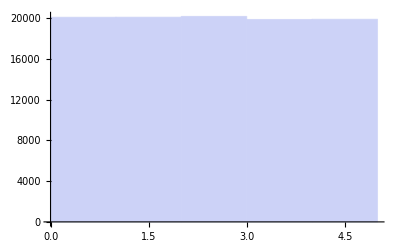

```mathematica
Histogram[t]
```

```mathematica
Tally[t]
```

{{0,20065},{3,19848},{1,20072},{4,19868},{2,20147}}

```mathematica
N[Kurtosis[t]]
```

1.70311

```mathematica
N[Skewness[t]]
```

0.0067406

```mathematica
N[Variance[t]]
```

1.9965

```mathematica
N[Covariance[t]]
```

1.9965

```mathematica
t5=Module[{i, current, result},
current=1;
result={};
Monitor[
For[i=0,i<100000,i++,
AppendTo[result,Middle[IntegerDigits[current-1,3]]];
current *=5*5;
],
i];
result
]
```

{0,2,0,0,2,1,1,1,0,1,0,2,1,1,1,0,1,0,0,1,2,2,2,0,1,1,2,0,2,0,0,1,1,0,2,0,2,1,1,0,2,1,0,0,1,1,0,2,2,0,1,2,1,2,1,0,1,1,0,1,2,2,1,2,2,2,0,1,2,1,2,2,0,2,1,1,1,1,0,2,0,0,2,0,2,2,2,1,0,2,1,1,1,2,1,1,0,2,0,2,2,2,1,1,1,1,0,0,0,0,1,1,0,2,0,1,2,1,2,1,2,0,2,0,0,0,1,1,1,2,0,1,0,0,1,0,2,1,1,0,0,2,0,1,0,0,0,1,1,2,0,0,1,0,1,1,0,1,2,1,2,1,1,1,1,2,2,1,2,1,2,2,2,2,2,2,1,2,1,1,1,1,2,1,1,0,0,0,1,1,2,0,0,2,1,2,2,0,0,2,1,1,2,0,0,2,0,1,0,0,1,2,2,1,2,0,2,2,2,0,2,2,2,0,2,0,2,2,2,2,1,1,2,1,2,1,«99528»,2,1,2,0,0,0,0,0,2,0,0,0,2,0,2,1,2,2,2,1,2,1,0,2,0,2,1,2,0,2,0,2,1,1,2,2,2,1,1,2,0,2,2,1,1,2,0,1,0,2,1,2,2,2,1,0,2,0,1,0,1,1,2,1,2,1,0,2,1,1,1,2,0,1,2,1,1,1,0,0,0,1,2,1,2,1,2,0,0,2,0,0,1,0,1,0,0,1,0,1,2,0,1,0,0,1,1,1,1,0,2,1,1,0,0,2,2,1,1,0,0,1,2,1,0,1,2,1,1,0,0,0,0,1,2,2,2,0,2,2,2,1,1,1,0,2,2,1,1,2,0,1,0,1,0,1,1,0,1,2,2,0,0,1,2,2,0,1,2,0,1,1,0,2,0,2,0,1,1,0,2,1,1,0,2,0,1,2,0,2,2,1,2,2,1,0,1,0,1,0,2,2,1,0,2,1,2,0,0,0,1,2,0,0,0,0,0,1,2,2,2,0,1,1,1,1,1,1,0,1,0,0,2,0,0,0}

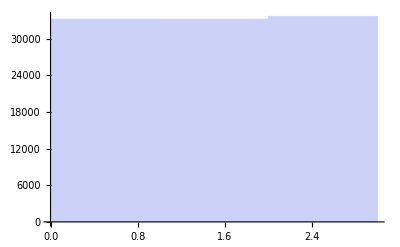

```mathematica
Histogram[t5]
```

```mathematica
N[Kurtosis[t5]]
```

1.49667

```mathematica
N[Skewness[t5]]
```

-0.00811094

```mathematica
mobiusInverse
```